```mathematica
FlatlandhalfspaceAlbedoProblemIsotropic`escapefs=FileNames["code/flatland/halfspace/albedoProblem/data/albedoproblem_escape*.txt"];
```

```mathematica
escapedatas=Last[Import[#,"Table"]]&/@FlatlandhalfspaceAlbedoProblemIsotropic`escapefs;
```

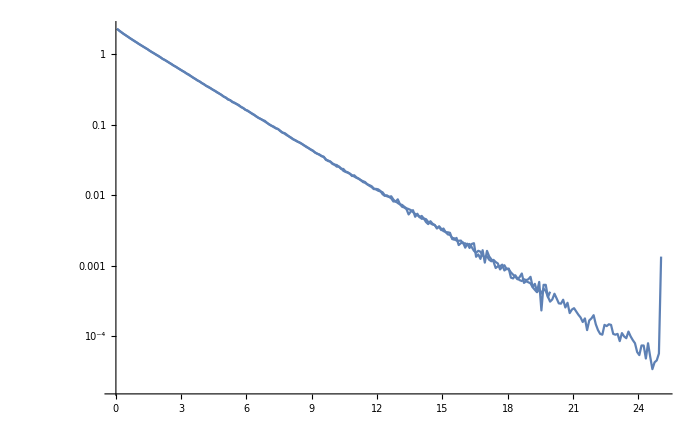

```mathematica
With[{i=10},
Show[
ListLogPlot[FlatlandhalfspaceAlbedoProblemIsotropic`plotpoints[FlatlandhalfspaceAlbedoProblemIsotropic`simulationswhitesky[[i,3,13]],0.1],Joined->True],
ListLogPlot[ FlatlandhalfspaceAlbedoProblemIsotropic`plotpoints[ Pi escapedatas[[i]],0.1],Joined->True]
]
]
```